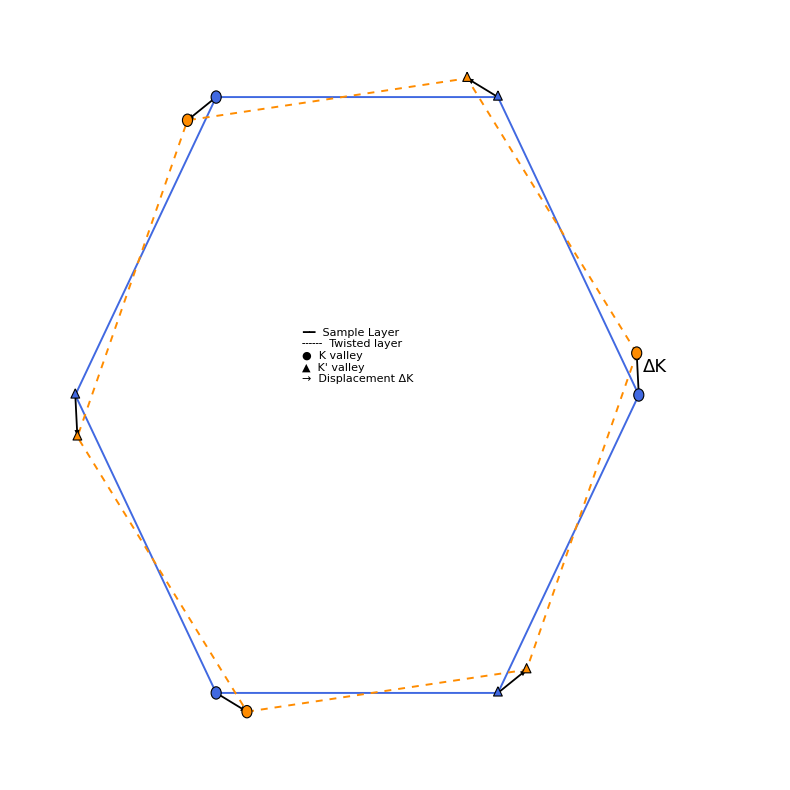

```mathematica
a=1.0;
thetaDeg=7;
theta=thetaDeg Degree;

Kmag=4 Pi/(3 a);
qmag=2 Kmag Sin[theta/2];

layer1=RGBColor[0.255,0.412,0.882]; 
layer2=RGBColor[1.0,0.549,0.0];     


angles=Table[i Pi/3,{i,0,5}];

Kref=Kmag {Cos[#],Sin[#]}&/@angles;

Ktwisted=(rot[theta].#)&/@Kref;

(*Alternating K and K' labels*)
valleyTau={1,-1,1,-1,1,-1};

(*Helper functions*)valleyMarker[1,colour_,size_:0.018]:={EdgeForm[Directive[Black,Thin]],FaceForm[colour],Disk[#,size]}&;

valleyMarker[-1,colour_,size_:0.018]:={EdgeForm[Directive[Black,Thin]],FaceForm[colour],Polygon[#+size {{0,1},{-0.866,-0.5},{0.866,-0.5}}]}&;

arrowGraphic[p1_,p2_,colour_:Black,thickness_:0.003]:={colour,AbsoluteThickness[1.3],Arrowheads[0.025],Arrow[{p1,p2}]};

drawCone[centre_,colour_,valley_,radius_:0.085]:={{Opacity[0.20,colour],EdgeForm[{colour,AbsoluteThickness[1.2]}],Disk[centre,radius]},{EdgeForm[{Black,AbsoluteThickness[0.5]}],FaceForm[colour],If[valley==1,Disk[centre,0.035],Polygon[(centre+#)&/@(0.040 {{0,1},{-Sqrt[3]/2,-1/2},{Sqrt[3]/2,-1/2}})]]}};

(*Panel A,named as there was a Panel B which has since been removed*)

closedRef=Append[Kref,First[Kref]];
closedTwisted=Append[Ktwisted,First[Ktwisted]];

hexagonsA={{layer1,AbsoluteThickness[1.4],Line[closedRef]},{layer2,Dashed,AbsoluteThickness[1.4],Line[closedTwisted]}};

valleyGraphic[point_,tau_,colour_,size_]:=If[tau==1,{EdgeForm[Directive[Black,Thin]],FaceForm[colour],Disk[point,size]},{EdgeForm[Directive[Black,Thin]],FaceForm[colour],Polygon[point+#&/@(size {{0,1},{-Sqrt[3]/2,-1/2},{Sqrt[3]/2,-1/2}})]}];

valleysA=Flatten[Table[valleyGraphic[Kref[[i]],valleyTau[[i]],layer1,0.075],{i,1,6}]~Join~Table[valleyGraphic[Ktwisted[[i]],valleyTau[[i]],layer2,0.075],{i,1,6}],2];

displacementsA=Table[{Black,AbsoluteThickness[1.3],Arrowheads[0.018],Arrow[{Kref[[i]],Ktwisted[[i]]}]},{i,1,6}];

mid=(Kref[[1]]+Ktwisted[[1]])/2;

legendInsideA=Framed[Style[Column[{Row[{Style["━━",layer1],"  Sample Layer"}],Row[{Style["╌╌╌",layer2],"  Twisted layer"}],Row[{Style["●",GrayLevel[0.5],16],"  K valley"}],Row[{Style["▲",GrayLevel[0.5],16],"  K' valley"}],Row[{Style["→",Black,18],"  Displacement ΔK"}]},Alignment->Left,Spacings->0.6],FontFamily->"Times New Roman",FontSize->18,FontColor->Black],Background->White,FrameStyle->LightGray,FrameMargins->8];

panelA=Graphics[{hexagonsA,displacementsA,valleysA,Black,Text[Style[TraditionalForm[ΔK],18],mid+{0.25,0.08}],Inset[legendInsideA,Scaled[{0.4,0.6}],{Left,Top}]},Frame->False,Axes->False,AspectRatio->1,PlotRange->All,ImagePadding->{{45,20},{35,55}},ImageSize->790];


panelA
```

```mathematica
Export["QTM_valley_geometry.png",panelA,ImageResolution->400];
```